#### FWHM of X - ray pulse

```mathematica
FWHM=Sqrt[2 Log[2]]σ
```

6.93147×10^-7

```mathematica
σ=N[FWHM/(2Sqrt[2 Log[2]])]/.FWHM->1 10^-6(*in meters*)
```

4.24661×10^-7

```mathematica
σ=(1 10^-6)/2.355
```

4.24628×10^-7

#### X - ray intensity distribution

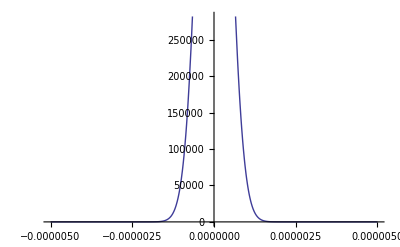

```mathematica
Plot[PDF[NormalDistribution[0,σ] ,x],{x,-5 10^-6,5 10^-6}]
```

```mathematica
numberOfPhotons=10^12;
```

```mathematica
NIntegrate[ numberOfPhotons PDF[NormalDistribution[0,σ] ,x],{x,-5 10^-6,5 10^-6}]
```

1.×10^12

```mathematica
numberOfXrayPhotonsInSample=NIntegrate[numberOfPhotons PDF[NormalDistribution[0,σ] ,x],{x,-25 10^-9,25 10^-9}](*number of photons in LCLS pulse interacting with Xe-cluster*)
```

4.69447×10^10

```mathematica
crossSectionOfXeAtom=3 10^-18;(*in cm^2*)
```

```mathematica
crossSectionOfXeAtom2=3 10^-18 10^-4 (*in m^2*)
```

3/10000000000000000000000

```mathematica
numberOfAbsorbedPhotons=(numberOfXrayPhotonsInSample*crossSectionOfXeAtom)/(625 10^-14(*in cm^2*)) (*units???*)
```

22533.5

```mathematica
eVinXray=numberOfAbsorbedPhotons*837(*absorbed X-ray energy in eV*)
```

1.88605×10^7

#### IR intensity distribution

```mathematica
σIR=(40 10^-6)/2.355
```

0.0000169851

```mathematica
intensityIR=2 10^15 (*watt cm^-2*);
```

```mathematica
pulseLengthIR = 70 10^-15 (*seconds*)
```

7/100000000000000

```mathematica
photonEnergy=1.5 (*electronvolt*)*1.60218 10^-19(*in Joule*)
```

2.40327×10^-19

```mathematica
numberOfIRphotons=intensityIR/photonEnergy pulseLengthIR (*per cm^-2*)
```

5.8254×10^20

```mathematica
(numberOfIRphotons *photonEnergy)/pulseLengthIR(*sanity check watt cm^-2*)
```

2.×10^15

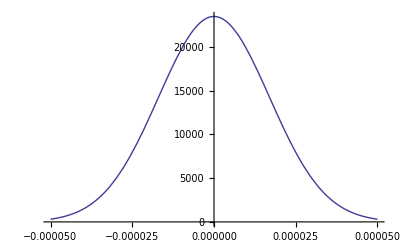

```mathematica
Plot[PDF[NormalDistribution[0,σIR] ,x],{x,-60 10^-6,60 10^-6}]
```

```mathematica
NIntegrate[ numberOfIRphotons PDF[NormalDistribution[0,σ] ,x],{x,-5 10^-6,5 10^-6}]
```

5.8254×10^20

```mathematica
numberOfIRphotonsInSample=NIntegrate[numberOfIRphotons PDF[NormalDistribution[0,σ] ,x],{x,-25 10^-9,25 10^-9}](*number of photons in LCLS pulse interacting with Xe-cluster*)
```

2.73472×10^19

```mathematica
crossSectionOfXeAtomIR=0.3(*in 10^20 m^2*)
```

0.3

```mathematica
numberOfAbsorbedPhotonsIR=(numberOfIRphotonsInSample*crossSectionOfXeAtomIR)/(62500 (*cluster size in Α^2*))(*photons*)
```

1.31266×10^14

```mathematica
eVinIR=numberOfAbsorbedPhotonsIR*1.5(*absorbed IR energy in eV*)
```

1.969×10^14

```mathematica
eVinXray/eVinIR
```

9.57875×10^-8